```mathematica
SetDirectory[NotebookDirectory[]];
```

## RandU

Example of RandU in a 3D space with the 15 horizontal lines.

```mathematica
SeedRandom[Method->{"Congruential","Multiplier"->65539,"Increment"->0,"Modulus"->2^ 31}]
RandomList = Table[{RandomReal[],RandomReal[],RandomReal[]},{i,0,10000}];
ListPointPlot3D[RandomList]
```

-Graphics3D-

## Additional analysis of RNG test

Read in the chi squared values with cumulative probability j/n for the jth chi squared value. And calculate the difference with the real chi squared distribution (red line).

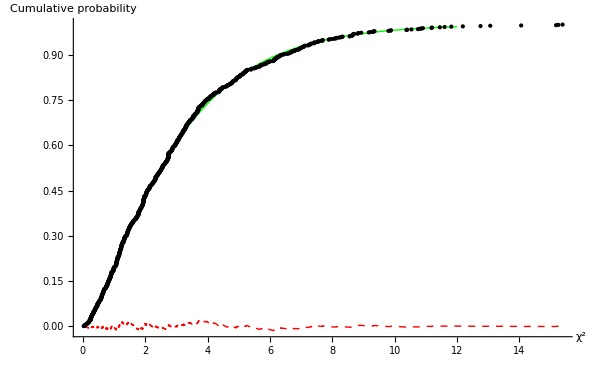

```mathematica
KSTestList = Import["chi2_data.dat"];
DifferenceList=Join[Partition[Table[KSTestList[[i,1]],{i,1,Length[KSTestList]}],1],Partition[Table[KSTestList[[i,2]]-CDF[ChiSquareDistribution[3],KSTestList[[i,1]]],{i,1,Length[KSTestList]}],1],2];
Show[ListPlot[DifferenceList,Joined->True, PlotStyle->Directive[Thick,Dashed,Red]],
Plot[CDF[ChiSquareDistribution[3],x],{x,0,12},PlotStyle->Directive[Thick,Green]],ListPlot[KSTestList,PlotStyle->Directive[Dashed,Black]],AxesLabel->{"χ^2","Cumulative probability"},PlotRange->All]
```

Norm (squared) and standard deviation of the norm (squared), together with a histogram indicating this is probably normally distributed.

```mathematica
MTNormList=Flatten[Import["norm_data.dat"]];
Mean[MTNormList]
StandardDeviation[MTNormList]
```

19960.

656.123

```mathematica
Histogram[MTNormList,100,PlotRange->All]
```

-Graphics-